```mathematica
ClearAll["Global`*"]
```

```mathematica
dxdt= ExpandAll[c3 (r B (1 - B/k) - b B^2 / (a^2 + B^2))/.{B->x/c1}]
```

(c3 r x)/c1-(c3 r x^2)/(c1^2 k)-(b c3 x^2)/(a^2 c1^2+x^2)

```mathematica
dxdt2=Expand[dxdt/.{c1->1/a,c3->1/b}]
```

(a r x)/b-(a^2 r x^2)/(b k)-x^2/(1+x^2)

```mathematica
FullSimplify[(/.{b ->a r/R})/.{a->k/(Q R)}]
```

x (R-x/Q-x/(1+x^2))

```mathematica
Simplify[((a r x)/b-(a^2 r x^2)/(b k))/(a r/b)]
```

x-(a x^2)/k

```mathematica
dxdt3=ρ x(1-x/γ )-x^2/(1+x^2)
```

```mathematica
FullSimplify[-x^2/(1+x^2)+x (1-x/γ) ρ]
```

x (-x/(1+x^2)+ρ-(x ρ)/γ)

```mathematica
Plot[(-x/(1+x^2)+ρ-(x ρ)/γ)/.{ρ->1,γ->1},{x,0,10}]
```

```mathematica
Solve[-x/(1+x^2)+ρ-(x ρ)/γ==0,γ]
```

{{γ→((x+x^3) ρ)/(-x+ρ+x^2 ρ)}}

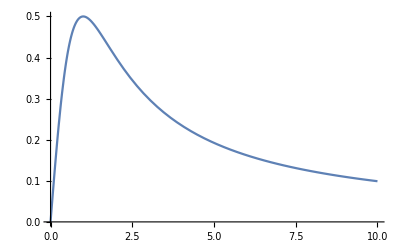

```mathematica
Plot[x/(1+x^2),{x,0,10}]
```

```mathematica
FullSimplify[Solve[dxdt3/x==0,x],Assumptions->{γ>0}]
```

{{x→1/6 (2 γ+(2 2^(1/3) (3 ρ+γ (3-γ ρ)))/((9 γ^2 ρ^2-18 γ ρ^3-2 γ^3 ρ^3+√(ρ^3 (γ^2 ρ (9 γ-2 (9+γ^2) ρ)^2+4 (3 ρ+γ (3-γ ρ))^3)))^(1/3))-(2^(2/3) (9 γ^2 ρ^2-18 γ ρ^3-2 γ^3 ρ^3+√(ρ^3 (γ^2 ρ (9 γ-2 (9+γ^2) ρ)^2+4 (3 ρ+γ (3-γ ρ))^3)))^(1/3))/ρ)},{x→1/12 (4 γ+(4 (-2)^(1/3) (-3 γ+(-3+γ^2) ρ))/((9 γ^2 ρ^2-18 γ ρ^3-2 γ^3 ρ^3+√(ρ^3 (γ^2 ρ (9 γ-2 (9+γ^2) ρ)^2+4 (3 ρ+γ (3-γ ρ))^3)))^(1/3))+(2^(2/3) (1-ⅈ √3) (9 γ^2 ρ^2-18 γ ρ^3-2 γ^3 ρ^3+√(ρ^3 (γ^2 ρ (9 γ-2 (9+γ^2) ρ)^2+4 (3 ρ+γ (3-γ ρ))^3)))^(1/3))/ρ)},{x→1/12 (4 γ+(2^(2/3) (1+ⅈ √3) (9 γ^2 ρ^2-18 γ ρ^3-2 γ^3 ρ^3+√(ρ^3 (γ^2 ρ (9 γ-2 (9+γ^2) ρ)^2+4 (3 ρ+γ (3-γ ρ))^3)))^(1/3))/ρ+((-3 γ+(-3+γ^2) ρ) Root[128+#1^3&,2])/((9 γ^2 ρ^2-18 γ ρ^3-2 γ^3 ρ^3+√(ρ^3 (γ^2 ρ (9 γ-2 (9+γ^2) ρ)^2+4 (3 ρ+γ (3-γ ρ))^3)))^(1/3)))}}

```mathematica
lhs = x/(1+x^2)
```

x/(1+x^2)

```mathematica
FullSimplify[D[lhs,x]/.{x->6}]
```

-35/1369

```mathematica
lhs/.x->6
```

6/37

```mathematica
NSolve[6/37==a -35/1369 6 ]
```

{{a→0.315559}}

```mathematica
-35/1369
```

-35/1369

```mathematica
N[-35/1369]
```

-0.0255661

```mathematica
rhs = FullSimplify[ρ(1-x/γ)/.{γ->10 }]
```

ρ-(x ρ)/10

```mathematica
D[lhs,x]/.{x->4}
```

-15/289

```mathematica
Solve[-15/289==-ρ/10]
```

{{ρ→150/289}}

```mathematica
FindInstance[{(lhs==rhs),(D[lhs,x])==-ρ/10},{x,ρ}]
```

{{x→AlgebraicNumber[Root[5-5 #1^2+#1^3&,1],{0,1,0}],ρ→AlgebraicNumber[Root[5-5 #1^2+#1^3&,1],{990/10201,5250/10201,-970/10201}]}}

```mathematica
Solve[ρ-ρ/γ x==x/(1+x^2)/.{ρ->1/2,γ->10}]
```

{{x→2},{x→4-√11},{x→4+√11}}

```mathematica
NSolve[ρ-ρ/γ x==x/(1+x^2)/.{ρ->1/5,γ->10},Reals]
```

{{x→0.204078}}

```mathematica
Solve[ρ-ρ/γ x==x/(1+x^2)/.{ρ->0.38397073162746038,γ->10}]
```

{{x→0.437432},{x→4.78128-2.05257×10^-7 ⅈ},{x→4.78128+2.05257×10^-7 ⅈ}}

```mathematica
FullSimplify[D[rhs,x]]
```

-ρ/10

```mathematica
N[Solve[ρ-ρ/γ x==x/(1+x^2)/.{ρ->1,γ->10}]]
```

{{x→8.88908},{x→0.555458+0.903572 ⅈ},{x→0.555458-0.903572 ⅈ}}

```mathematica
Solve[D[lhs,x]==-ρ/10,x]/.ρ->5/4
```

{{x→-√3},{x→√3},{x→-√3},{x→√3}}

```mathematica
rhs
```

```mathematica
√(5-4 ρ)==0
```

√(5-4 ρ)==0

```mathematica
Solve[√(5-4 ρ)==0,{ρ}]
```

{{ρ→5/4}}

```mathematica
sls=x/.Solve[lhs==rhs,x]
```

{10/3-(30 ρ-97 ρ^2)/(3 ρ (-450 ρ^2+1090 ρ^3+3 √3 √(1000 ρ^3-2200 ρ^4-4970 ρ^5+10201 ρ^6))^(1/3))+((-450 ρ^2+1090 ρ^3+3 √3 √(1000 ρ^3-2200 ρ^4-4970 ρ^5+10201 ρ^6))^(1/3))/(3 ρ),10/3+((1+ⅈ √3) (30 ρ-97 ρ^2))/(6 ρ (-450 ρ^2+1090 ρ^3+3 √3 √(1000 ρ^3-2200 ρ^4-4970 ρ^5+10201 ρ^6))^(1/3))-((1-ⅈ √3) (-450 ρ^2+1090 ρ^3+3 √3 √(1000 ρ^3-2200 ρ^4-4970 ρ^5+10201 ρ^6))^(1/3))/(6 ρ),10/3+((1-ⅈ √3) (30 ρ-97 ρ^2))/(6 ρ (-450 ρ^2+1090 ρ^3+3 √3 √(1000 ρ^3-2200 ρ^4-4970 ρ^5+10201 ρ^6))^(1/3))-((1+ⅈ √3) (-450 ρ^2+1090 ρ^3+3 √3 √(1000 ρ^3-2200 ρ^4-4970 ρ^5+10201 ρ^6))^(1/3))/(6 ρ)}

```mathematica
NSolve[sls[[1]]==sls[[3]]]
```

{{ρ→-0.456289},{ρ→0.383971}}

```mathematica
dxdt3/.γ->10
```

```mathematica
sls=x/.FullSimplify[Solve[-x/(1+x^2)+(1-x/10)  ρ==0,x,Cubics->True],Assumptions->ρ>0]
```

{1/3 (10+(30-97 ρ)/((10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3))-((10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3))/ρ),1/6 (20+((1+ⅈ √3) (-30+97 ρ))/((10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3))+((1-ⅈ √3) (10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3))/ρ),1/6 (20+((1-ⅈ √3) (-30+97 ρ))/((10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3))+((1+ⅈ √3) (10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3))/ρ)}

```mathematica
z1=(10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3)
```

```mathematica
FullSimplify[(sls[[1]]*3-10 )/ z1]
```

-1/ρ+(30-97 ρ)/((10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(2/3))

```mathematica
(10 (45-109 ρ) ρ^2+3 √3 √(ρ^3 (1000+ρ (-2200+ρ (-4970+10201 ρ)))))^(1/3)==z1
```

True

```mathematica
FullSimplify[D[dxdt3,x]/.{γ->10}]
```

-(2 x)/((1+x^2)^2)+ρ-(x ρ)/5